```mathematica
FullSimplify[Exp[ⅈ(2π)/λ z]/(ⅈ(2π)/λ z)Exp[ⅈ(2π)/λ(ξ^2+η^2)/(2z)]E0∫_0^(2a) ∫_(1/4 y-a)^(a-1/4 y) Exp[-ⅈ(2π)/λ(x*ξ+y*η)/z]ⅆxⅆy]
```

-(ⅈ ⅇ^((ⅈ π (2 z^2+η^2+ξ^2))/(z λ)) E0 z λ^3 ((ⅇ^(-(2 ⅈ a π ξ)/(z λ))-ⅇ^(-(ⅈ a π (4 η+ξ))/(z λ)))/(4 η-ξ)-(ⅇ^(-(ⅈ a π (4 η-ξ))/(z λ)) (-1+ⅇ^((ⅈ a π (4 η+ξ))/(z λ))))/(4 η+ξ)))/(2 π^3 ξ)

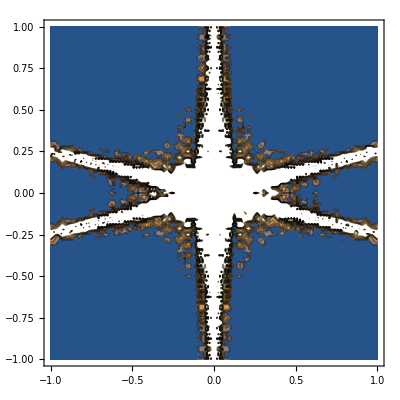

```mathematica
Energy[ξ_,η_,z_,λ_,a_,E0_]:=-1/(2.* π^3* ξ)ⅈ ⅇ^((ⅈ π (2.* z^2+η^2+ξ^2))/(z* λ)) E0 *z *λ^3 ((ⅇ^(-(2.* ⅈ *a* π* ξ)/(z* λ))-ⅇ^(-(ⅈ* a *π (4.*η+ξ))/(z *λ)))/(4.*η-ξ)-(ⅇ^(-(ⅈ* a* π (4.*η-ξ))/(z* λ)) (-1.+ⅇ^((ⅈ* a* π (4.*η+ξ))/(z* λ))))/(4.*η+ξ));
Intensity[ξ_,η_,z_,λ_,a_,E0_]:=Power[Abs[Energy[ξ,η,z,λ,a,E0]],2.];
ContourPlot[Intensity[ξ,η,10.,5.*Power[10.,-7.],5.*Power[10.,-3.],1.*Power[10,16]],{ξ,-1.,1.},{η,-1.,1.}]
```